Angle of Repose
Shiva Shahrokhi and Aaron T. Becker
when granular media is dropped in a pile, it forms a cone.  The maximum slope of the cone depends on the material used, but is very repeatable (due to CLT) and is called the angle of repose.  
Robot swarms, such as the Kilobot, also have an angle of repose

https://en.wikipedia.org/wiki/Angle_of_repose
The angle of repose, or critical angle of repose,[1] of a granular material is the steepest angle of descent or dip relative to the horizontal plane to which a material can be piled without slumping. At this angle, the material on the slope face is on the verge of sliding. The angle of repose can range from 0° to 90°.

```mathematica
l = 1; (*width of bar holding material*)
Manipulate[Module[{a,b,p,c,lside,h,d,Area},
Graphics[ {
a= l/2*{Cos[θ],Sin[θ]};
b = l/2*{Cos[α],Sin[α]};
c = l/2*{1,0};
p =  l/10*{Sin[θ],-Cos[θ]};
h = l/2;
d = l/2;

White,Rectangle[{-l,-l},{l,2}],

Pink,(*Rotate[Rectangle[{-l/2,-.1},{l/2,0}],-θ π/180,{0,0}]}],*)
Polygon[{a,a+p,-a+p,-a}],
(* draw piles of stuff on ground*)
Brown,Polygon[{{-l/2Cos[θ]-h Cos[α],-d-h},{-l/2Cos[θ],h Sin[α]-h-d},{-l/2Cos[θ]+h Cos[α],-h-d}}],
Brown,Polygon[{{l/2Cos[θ]-h Cos[α],-d-h},{l/2Cos[θ],h Sin[α]-h-d},{l/2Cos[θ]+h Cos[α],-h-d}}],
(*granular media*)
If[α>Abs[θ],
{lside=(l Sin[θ+α])/Sin[π-2α];Polygon[{a,lside{Cos[α],Sin[α]}-a,-a}]},lside=0;],
(*Black,Text[N[{l/2Cos[θ]+h Cos[α],-h-d}],{0,0}],*)

(*draw angle of repose*)
Black,Line[{-a+c/2,-a,-a+ l/4*{Cos[α],Sin[α]}}],
Black,Line[{a-c/2,a,a+ l/4*{-Cos[α],Sin[α]}}],
Circle[-a,l/6,{0,α}],
Circle[a,l/6,{π,π-α}],
(* measure weight of granular media  (proportional to area of triangle)*)
Area = 1/2 lside l Sin[α-θ];
Black,Text[StringForm["Area = ``",N[Round[Area,0.01]]],{0,-1/2}],

(*measure torque of granular media*)
(*draw a scale*)
Blue,PointSize[Large],Point[{0,0}]


}]],
{{α,π/4,"Angle of Repose"} ,0,5π/12,π/36,Appearance->"Labeled"},
{{θ,0} ,- 5π/12, 5π/12,π/36,Appearance->"Labeled"},
(*add setter bar so you can select the material to use.  Should change the angle or repose and the color of the granular media*)
{material,{"sand","salt","corn","wheat"}}
]
```

Global`Area::shdw: Symbol Area appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

### Compute the Torque about the center of the object

```mathematica
heightBottom[x_,θ_]:=Tan[θ]x;
heightTop[x_,α_,l_,θ_] := Min[  Tan[α]x+l/2(Cos[θ]Tan[α]-Sin[θ]), -Tan[α]x+l/2(Cos[θ]Tan[α]+Sin[θ])]; 
(*Torque[θ_,α_,l_] := ∫_(-l/2Cos[θ])^(l/2Cos[θ]) x(heightTop[x,α,l,θ]-heightBottom[x,θ])ⅆx*)
Torque1[θ_,α_,l_] := ∫_(-l/2Cos[θ])^(l/2Cos[θ]) x(heightTop[x,α,l,θ]-heightBottom[x,θ])ⅆx
```

Angle of repose for  a list of materials :
  Ashes 40
Asphalt 30
Bark

```mathematica
FullSimplify[x(heightTop[x,α,l,θ]-heightBottom[x,θ])]
```

x (Min[1/2 Sec[α] (-2 x Sin[α]+Sin[α+θ]),1/2 (-Sin[θ]+(2 x+Cos[θ]) Tan[α])]-x Tan[θ])

```mathematica
1/2 Min[ Sec[α] (-2 x Sin[α]+Sin[α+θ]), (-Sin[θ]+(2 x+Cos[θ]) Tan[α])]-x Tan[θ]
```

1/2 Min[Sec[α] (-2 x Sin[α]+Sin[α+θ]),-Sin[θ]+(2 x+Cos[θ]) Tan[α]]-x Tan[θ]

```mathematica
Manipulate[Plot[{heightTop[x,α,1,θ],heightBottom[x,θ]},{x,-1,1}],{{α,π/4,"Angle of Repose"} ,0,5π/12,π/36,Appearance->"Labeled"},
{{θ,0} ,- 5π/12, 5π/12,π/36,Appearance->"Labeled"}]
```

```mathematica
Clear[l]
a= l/2*{Cos[θ],Sin[θ]};
lside=(l Sin[θ+α])/Sin[π-2α];FullSimplify[lside{Cos[α],Sin[α]}-a]
xMid = (*Cos[α](l Sin[θ+α])/Sin[π-2α]-l/2Cos[θ]*) (l Cot[α] Sin[θ])/2;
(*FullSimplify[ Cos[α](l Sin[θ+α])/Sin[π-2α]-l/2Cos[θ]] = (l Cot[α] Sin[θ])/2*)
```

{1/2 l Cot[α] Sin[θ],1/2 l Cos[θ] Tan[α]}

```mathematica
heightTop[x_,α_,l_,θ_] := Min[  Tan[α]x+l/2(Cos[θ]Tan[α]-Sin[θ]), -Tan[α]x+l/2(Cos[θ]Tan[α]+Sin[θ])];
```

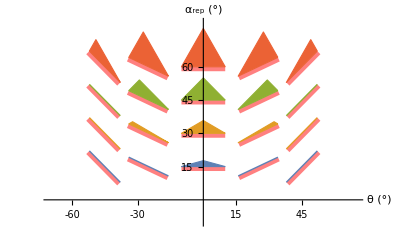
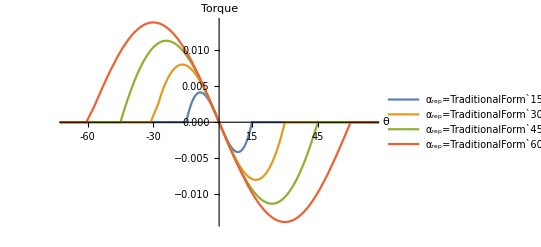
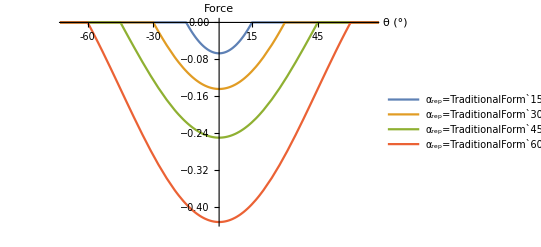
### Plot force and torque -Graphics--Graphics--Graphics-

```mathematica
Torque[θ_,α_,l_] :=If[Cos[θ]<Cos[α],0, ∫_(-l/2Cos[θ])^((l Cot[α] Sin[θ])/2) x(Tan[α]x+l/2(Cos[θ]Tan[α]-Sin[θ])  -Tan[θ]x)ⅆx+
 ∫_((l Cot[α] Sin[θ])/2)^(l/2Cos[θ]) x(-Tan[α]x+l/2(Cos[θ]Tan[α]+Sin[θ])-Tan[θ]x)ⅆx]
Force[θ_,α_,l_] :=If[Cos[θ]<Cos[α],0, ∫_(-l/2Cos[θ])^((l Cot[α] Sin[θ])/2) (Tan[α]x+l/2(Cos[θ]Tan[α]-Sin[θ])  -Tan[θ]x)ⅆx+
 ∫_((l Cot[α] Sin[θ])/2)^(l/2Cos[θ]) (-Tan[α]x+l/2(Cos[θ]Tan[α]+Sin[θ])-Tan[θ]x)ⅆx]
```

```mathematica
aDeg = {15,30,45,60};
as =aDeg π/180;
l=1;
Plot[Evaluate[Table[-Torque[θ π/180,a,1],{a,as}]],{θ,-90,90},

Ticks->{{-60,-45,-30,-15,15,30,45,60},Automatic},PlotRange-> {{-70,70},Automatic},PlotLegends->Placed[Table[StringForm["α_rep=``°",a],{a,aDeg}],{Left,Bottom}],AxesLabel->{"θ","Torque"}]
```

-Graphics-

```mathematica
aDeg = {15,30,45,60};
as =aDeg π/180;
l=1;
Plot[Evaluate[Table[-Force[θ π/180,a ,1],{a,as}]],{θ,-90,90},
Ticks->{{-60,-45,-30,-15,15,30,45,60},Automatic},PlotRange-> {{-70,70},Automatic},PlotLegends->Placed[Table[StringForm["α_rep=``°",a],{a,aDeg}],{Left,Bottom}],AxesLabel->{"θ (°)","Force"}]
```

-Graphics-

```mathematica
FullSimplify[If[Cos[θ]<Cos[α],0, ∫_(-l/2Cos[θ])^((l Cot[α] Sin[θ])/2) (Tan[α]x+l/2(Cos[θ]Tan[α]-Sin[θ])  -Tan[θ]x)ⅆx+
 ∫_((l Cot[α] Sin[θ])/2)^(l/2Cos[θ]) (-Tan[α]x+l/2(Cos[θ]Tan[α]+Sin[θ])-Tan[θ]x)ⅆx]]
```

If[Cos[θ]<Cos[α],0,∫_(1/2 (-l) Cos[θ])^(1/2 l Cot[α] Sin[θ]) (Tan[α] x+1/2 l (Cos[θ] Tan[α]-Sin[θ])-Tan[θ] x)ⅆx+∫_(1/2 l Cot[α] Sin[θ])^(1/2 l Cos[θ]) (-Tan[α] x+1/2 l (Cos[θ] Tan[α]+Sin[θ])-Tan[θ] x)ⅆx]

```mathematica
DrawGranular[θ_,α_,s_,colr_]:=Module[{a,p,h,d,lside},
l = 20;
a= l/2*{Cos[θ],Sin[θ]};
p =  l/10*{Sin[θ],-Cos[θ]};
h = l/2;
d = l/2;
{Pink,Polygon[{s+a,s+a+p,s+-a+p,s-a}],EdgeForm[{colr}],colr,
(*granular media*)
If[α>Abs[θ],
{lside=(l Sin[θ+α])/Sin[π-2α];Polygon[{s+a,s+lside{Cos[α],Sin[α]}-a,s-a}]},Line[{s+a,s-a}]]
}
]
aDeg = {15,30,45,60};
as =aDeg π/180;
l=1;
Plot[{},{θ,-90,90},Ticks->{{-60,-45,-30,-15,15,30,45,60},aDeg},PlotRange-> {{-70,70},{-10,80}},AxesLabel->{"θ (°)","α_rep (°)"},Prolog->{
Table[DrawGranular[theta π/180,aDeg⟦i⟧ π/180,{theta,aDeg⟦i⟧},ColorData[97,"ColorList"]⟦i⟧],{i,Length[aDeg]},{theta,{-45,-25,0,25,45}}]
}]
```

-Graphics-

Hardware Experiments

```mathematica
N[Sin[90 Degree]]
N[Sin[60 Degree]]
N[Sin[45 Degree]]
```

1.

0.866025

0.707107

```mathematica
Mean[{43.49, 29.02+13.24,11.45+28.98}]
```

42.06

```mathematica
Mean[{48.81,31.62+18.29,19.09+31.66}]
```

49.8233

```mathematica
vals45={67.34,47.28+15.42,32.05+29.65,17.44+43.35}
Mean[vals45]
```

{67.34,62.7,61.7,60.79}

63.1325

```mathematica
90-22.5
```

67.5

```mathematica
90-
```